```mathematica
SetDirectory[NotebookDirectory[]];
rawKernel=Import["./GeoLandscapes/Comoros_Kernel.csv"];
scaledKernel=1000*rawKernel;
rawCoordinates=Import["./GeoLandscapes/Comoros_Coordinates.csv"];
graph=WeightedAdjacencyGraph[rawKernel];
```

```mathematica
matrixPlotKernel=MatrixPlot[rawKernel,ColorFunction->"LakeColors"];
```

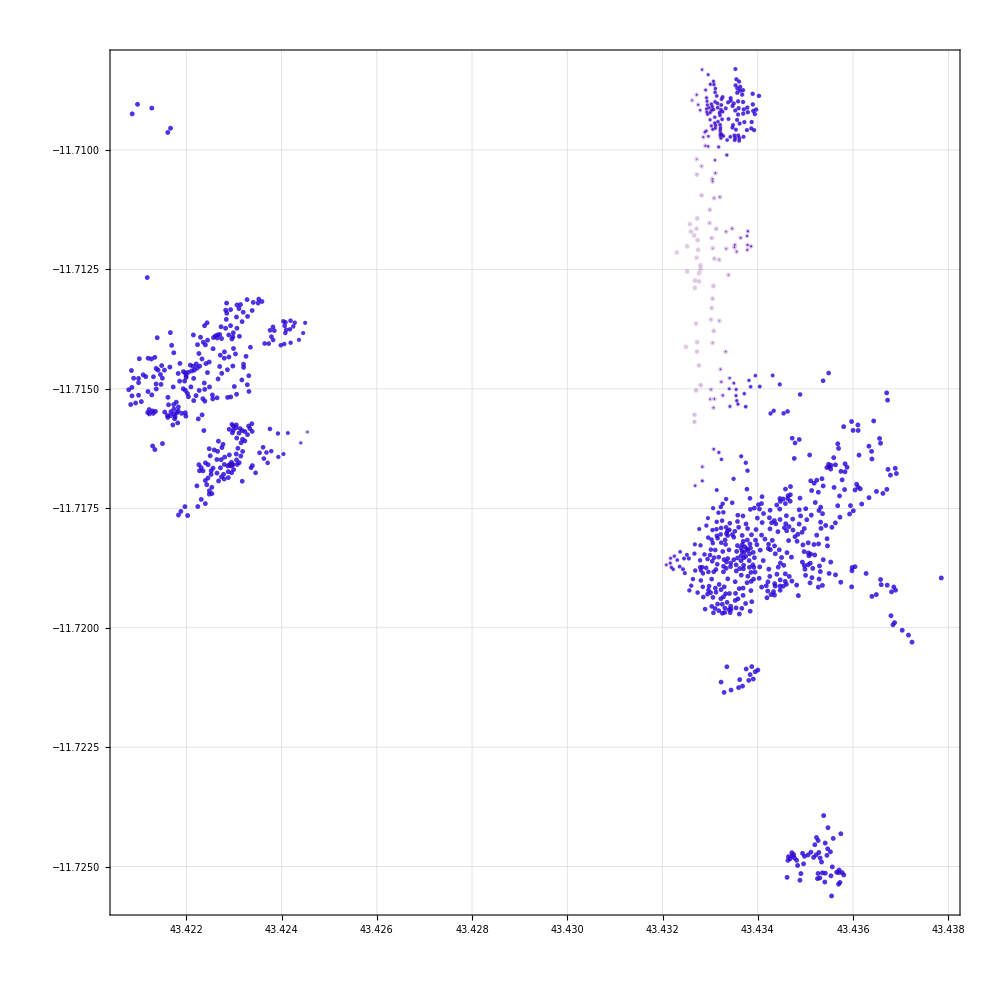

```mathematica
centralities=ClosenessCentrality[graph];
{minCentrality,maxCentrality}={centralities//Min,centralities//Max};
(**)
pointSizes=Rescale[#,{minCentrality,maxCentrality},{0.000001,.00005}]&/@centralities;
disks=Disk[#[[2]],#[[1]]]&/@({pointSizes,rawCoordinates}//Transpose);
scaledMap=Graphics[Flatten[{Blue,Opacity[.75],disks}],
AspectRatio->1,
Frame->True,
FrameStyle->Thick,
FrameTicksStyle->Directive[15],
GridLines->Automatic,
GridLinesStyle->Directive[Thick,Opacity[.5],LightGray],
ImageSize->750
];
(**)
pointSizes=ConstantArray[.00005,Length[centralities]];
disks=Disk[#[[2]],#[[1]]]&/@({pointSizes,rawCoordinates}//Transpose);
originalMap=Graphics[Flatten[{Purple,Opacity[.2],disks}],
AspectRatio->1,
Frame->True,
FrameStyle->Thick,
FrameTicksStyle->Directive[15],
GridLines->Automatic,
GridLinesStyle->Directive[Thick,Opacity[.35],LightGray]
];
Show[scaledMap,originalMap,ImageSize->1000]
```

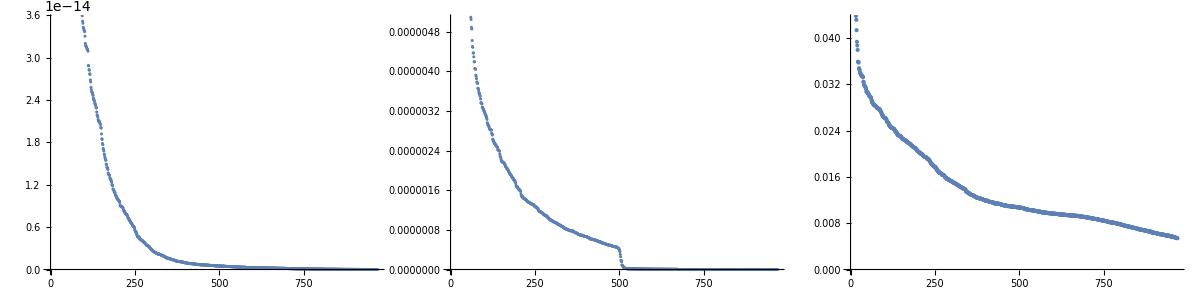

```mathematica
min=ListPlot[Sort[Min/@rawKernel]//Reverse];
med=ListPlot[Sort[Median/@ReplacePart[rawKernel,{i_,i_}->0]]//Reverse];
max=ListPlot[Sort[Max/@ReplacePart[rawKernel,{i_,i_}->0]]//Reverse];
Grid[{{min,med,max}}]
```